```mathematica
xi1={0,0};
xi2={0.353553390593274,0.353553390593274};
xi3={0.707106781186548,0};
xi4={0.707106781186548,0.500000000000000};
xi5={0.353553390593274,0.853553390593274};
xi6={0,0.500000000000000};
xi7={0,1};
xi8={0.353553390593274,1.35355339059327};
xi9={0.707106781186548,1};

yi1={0,0,0};
yi2={0.265165042944955,0.176776695296637,0};
yi3={0.530330085889911,0,0};
yi4={0.530330085889911,0.250000000000000,0.100000000000000};
yi5={0.265165042944955,0.426776695296637,0.100000000000000};
yi6={0,0.250000000000000,0.100000000000000};
yi7={0,0.500000000000000,0};
yi8={0.265165042944955,0.676776695296637,0};
yi9={0.530330085889911,0.500000000000000,0};

x1={7.39167416661636*^-19,-7.70652172306097*^-17};
x2={0.353553385550912,0.138060748464882};
x3={0.707106781186548,1.53034610285594*^-18};
x4={0.707106785387311,0.500000005283682};
x5={0.353553388722155,0.638060753685781};
x6={4.20076343949820*^-9,0.500000005283682};
x7={2.92883530207801*^-17,1};
x8={0.353553385550911,1.13806074846488};
x9={0.707106781186548,1};

y1={4.00130523437597*^-18,7.04915346958963*^-18,2.73838206066634*^-17};
y2={0.265165035893017,0.272913202937561,-2.82346451752450*^-9};
y3={0.530330085889911,3.04393048834494*^-17,-1.38694015490858*^-17};
y4={0.530330097596864,0.250000009525689,0.432574980134039};
y5={0.265165046832367,0.522913212431764,0.432574977310575};
y6={1.17069532291768*^-8,0.250000009525689,0.432574980134040};
y7={-1.92735032105306*^-19,0.500000000000000,5.31939284345514*^-18};
y8={0.265165035893017,0.772913202937561,-2.82346446980097*^-9};
y9={0.530330085889911,0.500000000000000,6.09635828068521*^-18};

t1 = y3 - y1;
t2 = y7 - y1;
t1x = x3 - x1;
t2x = x7 - x1;
```

```mathematica
g1[{x01_,x02_,x03_}] = {x01,x02,x03} + t1;
```

```mathematica
g2[{x01_,x02_,x03_}] ={x01,x02,x03} + t2;
g1x[{x01_,x02_}] = {x01,x02} + t1x;
g2x[{x01_,x02_}] = {x01,x02} + t2x;
```

```mathematica
g1[y1]-y3
```

{0.,0.,-3.08149×10^-33}

```mathematica
g2[y1]-y7
```

{2.88889×10^-34,0.,0.}

```mathematica
{0.,0.,0.}
g1x[x1] - x3
```

{0.,0.,0.}

{0.,1.34815×10^-33}

```mathematica
g2x[x1] - x7
```

{0.,-1.11022×10^-16}

```mathematica
baseColor=GrayLevel[0.8];

IStep = 3; JStep = 3;
(* Initial y *)
dPolyyi = Array[dPyi,{IStep,JStep}];
For[j=1,j<JStep+1,j++ ,For[i = 1,i< IStep+1,i++,dPyi[i,j]={Polygon[{Nest[g1,Nest[g2,yi1,j],i],Nest[g1,Nest[g2,yi2,j],i],Nest[g1,Nest[g2,yi5,j],i], Nest[g1,Nest[g2,yi6,j],i]}],Polygon[{Nest[g1,Nest[g2,yi2,j],i],Nest[g1,Nest[g2,yi3,j],i],Nest[g1,Nest[g2,yi4,j],i], Nest[g1,Nest[g2,yi5,j],i]}], Polygon[{Nest[g1,Nest[g2,yi5,j],i],Nest[g1,Nest[g2,yi6,j],i],Nest[g1,Nest[g2,yi7,j],i], Nest[g1,Nest[g2,yi8,j],i]}], Polygon[{Nest[g1,Nest[g2,yi4,j],i],Nest[g1,Nest[g2,yi5,j],i],Nest[g1,Nest[g2,yi8,j],i], Nest[g1,Nest[g2,yi9,j],i]}]}]]
fadedDPi=dPolyyi/. p_Polygon:>{Opacity[0.4],p};
fadedDPi[[2,2]]=dPolyyi[[2,2]];
Graphics3D[{EdgeForm[Opacity[0.1]],fadedDPi},Boxed->False]
```

-Graphics3D-

```mathematica
(* Final y *)
dPoly = Array[dP,{IStep,JStep}];
```

```mathematica
For[j=1,j<JStep+1,j++ ,For[i = 1,i< IStep+1,i++,dP[i,j]={Polygon[{Nest[g1,Nest[g2,y1,j],i],Nest[g1,Nest[g2,y2,j],i],Nest[g1,Nest[g2,y5,j],i], Nest[g1,Nest[g2,y6,j],i]}],Polygon[{Nest[g1,Nest[g2,y2,j],i],Nest[g1,Nest[g2,y3,j],i],Nest[g1,Nest[g2,y4,j],i], Nest[g1,Nest[g2,y5,j],i]}], Polygon[{Nest[g1,Nest[g2,y5,j],i],Nest[g1,Nest[g2,y6,j],i],Nest[g1,Nest[g2,y7,j],i], Nest[g1,Nest[g2,y8,j],i]}], Polygon[{Nest[g1,Nest[g2,y4,j],i],Nest[g1,Nest[g2,y5,j],i],Nest[g1,Nest[g2,y8,j],i], Nest[g1,Nest[g2,y9,j],i]}]}]]
```

```mathematica
(*Graphics3D[{EdgeForm[Opacity[.1]],Evaluate[dPoly]},Boxed->False] *)
fadedDP=dPoly/. p_Polygon:>{Opacity[0.4],p};
fadedDP[[2,2]]=dPoly[[2,2]];
Graphics3D[{EdgeForm[Opacity[0.1]],fadedDP},Boxed->False]
```

-Graphics3D-

```mathematica
(*color1light=Opacity[0.3,RGBColor[0.48,0.52,0.69]]; (*Blue-Grey*)
color4light=Opacity[0.3, RGBColor[0.91,0.90,0.82]]; (*Cream*)
color3light=Opacity[0.3, RGBColor[0.84,0.50,0.32]]; (*Orange*)
color2light=Opacity[0.3, RGBColor[0.39,0.20,0.25]];(*Burgundy*)
color1=RGBColor[0.48,0.52,0.69]; (*Blue-Grey*)
color4=RGBColor[0.91,0.90,0.82]; (*Cream*)
color3=RGBColor[0.84,0.50,0.32]; (*Orange*)
color2=RGBColor[0.39,0.20,0.25];*)(*Burgundy*)
background  = GrayLevel[0.8];
maincell = GrayLevel[0.6];
```

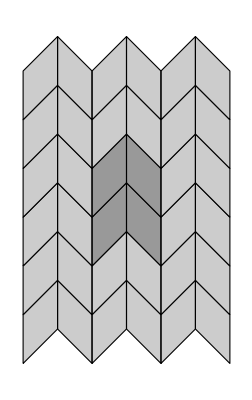

```mathematica
(* Initial x *)
dPolyxi2D=Table[{
background,Polygon[{Nest[g1x,Nest[g2x,xi1,j],i],Nest[g1x,Nest[g2x,xi2,j],i],Nest[g1x,Nest[g2x,xi5,j],i],Nest[g1x,Nest[g2x,xi6,j],i]}],
background,Polygon[{Nest[g1x,Nest[g2x,xi2,j],i],Nest[g1x,Nest[g2x,xi3,j],i],Nest[g1x,Nest[g2x,xi4,j],i],Nest[g1x,Nest[g2x,xi5,j],i]}],
background,Polygon[{Nest[g1x,Nest[g2x,xi5,j],i],Nest[g1x,Nest[g2x,xi6,j],i],Nest[g1x,Nest[g2x,xi7,j],i],Nest[g1x,Nest[g2x,xi8,j],i]}],
background,Polygon[{Nest[g1x,Nest[g2x,xi4,j],i],Nest[g1x,Nest[g2x,xi5,j],i],Nest[g1x,Nest[g2x,xi8,j],i],Nest[g1x,Nest[g2x,xi9,j],i]}]},
{i,1,IStep},{j,1,JStep}];
dPolyxi2D[[2,2]]={maincell,Polygon[{Nest[g1x,Nest[g2x,xi1,2],2],Nest[g1x,Nest[g2x,xi2,2],2],Nest[g1x,Nest[g2x,xi5,2],2],Nest[g1x,Nest[g2x,xi6,2],2]}],maincell,Polygon[{Nest[g1x,Nest[g2x,xi2,2],2],Nest[g1x,Nest[g2x,xi3,2],2],Nest[g1x,Nest[g2x,xi4,2],2],Nest[g1x,Nest[g2x,xi5,2],2]}],maincell,Polygon[{Nest[g1x,Nest[g2x,xi5,2],2],Nest[g1x,Nest[g2x,xi6,2],2],Nest[g1x,Nest[g2x,xi7,2],2],Nest[g1x,Nest[g2x,xi8,2],2]}],maincell,Polygon[{Nest[g1x,Nest[g2x,xi4,2],2],Nest[g1x,Nest[g2x,xi5,2],2],Nest[g1x,Nest[g2x,xi8,2],2],Nest[g1x,Nest[g2x,xi9,2],2]}]};
Graphics[{EdgeForm[{Black, Thin}],dPolyxi2D}]
```

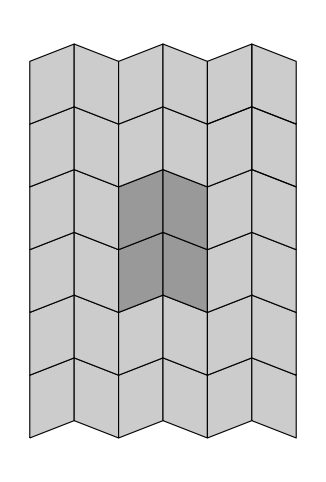

```mathematica
(* Final x *)
dPoly2D=Table[{
background,Polygon[{Nest[g1x,Nest[g2x,x1,j],i],Nest[g1x,Nest[g2x,x2,j],i],Nest[g1x,Nest[g2x,x5,j],i],Nest[g1x,Nest[g2x,x6,j],i]}],
background,Polygon[{Nest[g1x,Nest[g2x,x2,j],i],Nest[g1x,Nest[g2x,x3,j],i],Nest[g1x,Nest[g2x,x4,j],i],Nest[g1x,Nest[g2x,x5,j],i]}],
background,Polygon[{Nest[g1x,Nest[g2x,x5,j],i],Nest[g1x,Nest[g2x,x6,j],i],Nest[g1x,Nest[g2x,x7,j],i],Nest[g1x,Nest[g2x,x8,j],i]}],
background,Polygon[{Nest[g1x,Nest[g2x,x4,j],i],Nest[g1x,Nest[g2x,x5,j],i],Nest[g1x,Nest[g2x,x8,j],i],Nest[g1x,Nest[g2x,x9,j],i]}]},
{i,1,IStep},{j,1,JStep}];
dPoly2D[[2,2]]={maincell,Polygon[{Nest[g1x,Nest[g2x,x1,2],2],Nest[g1x,Nest[g2x,x2,2],2],Nest[g1x,Nest[g2x,x5,2],2],Nest[g1x,Nest[g2x,x6,2],2]}],maincell,Polygon[{Nest[g1x,Nest[g2x,x2,2],2],Nest[g1x,Nest[g2x,x3,2],2],Nest[g1x,Nest[g2x,x4,2],2],Nest[g1x,Nest[g2x,x5,2],2]}],maincell,Polygon[{Nest[g1x,Nest[g2x,x5,2],2],Nest[g1x,Nest[g2x,x6,2],2],Nest[g1x,Nest[g2x,x7,2],2],Nest[g1x,Nest[g2x,x8,2],2]}],maincell,Polygon[{Nest[g1x,Nest[g2x,x4,2],2],Nest[g1x,Nest[g2x,x5,2],2],Nest[g1x,Nest[g2x,x8,2],2],Nest[g1x,Nest[g2x,x9,2],2]}]};
Graphics[{EdgeForm[{Black, Thin}],dPoly2D}]
```